```mathematica
ClearAll["Global`*"]
w=2/3;
period=2*Pi/w;
A=1;
tmax=1000;
soln=ParametricNDSolve[{theta''[t]+(1/Q) * theta'[t]+Sin[theta[t]]==A  Cos[w t],theta[0]==0,theta'[0]==0},theta,{t,0,tmax},{Q}];
```

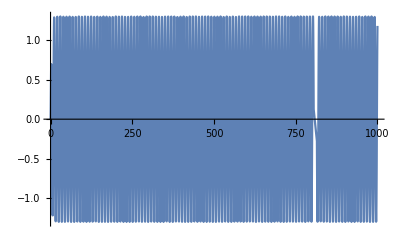

```mathematica
Q=1;
Plot[theta[Q][x]/.soln,{x,0,tmax}]
```

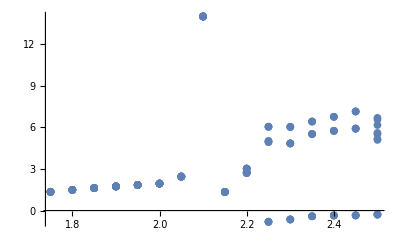

```mathematica
tdel=period;
length=Length[Table[x,{x,400,500,tdel}]];
res=20;
bifur=Flatten[Table[Transpose[{
ConstantArray[i/res,length],Flatten[Table[theta[i/res][x]/.soln,{x,400,500,tdel}]]}],
{i,35,50}],1];
ListPlot[bifur]
```